### code below runs simulation that generated data in Figure 4

```mathematica
ClearAll["Global`*"]
(*τ=3.4;*) τ=2.4; v10=1; s0=10^8;  b=200; a=3.5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001;
j1[t_,tl_]:=If[0<t<tl,1/tl,0];
sol := NDSolve[{
D[s1[t], t]==s0 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v10,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
 v2total = {v10}; stotal = {s0};
For[y=0, y<100,y++,
sol1=sol;
v10 = v2[T]/.sol1[[1,3]];
s0 = σ s1[T]/(1+ α s1[T])/.sol1[[1,1]];
v2total=Append[v2total, v10];
v20eq=Last[v2total];
stotal=Append[stotal, s0];
s0eq=Last[stotal]
];
(*dynamics cycle as τ increases parasite density*)
ListPlot[{v2total},Frame->True,FrameLabel->{{"parasite density",None},{"season","T=4, t_l=1"}}];
ListPlot[{stotal},Frame->True,FrameLabel->{{"host density",None},{"season","T=4, t_l=1"}}];
```

```mathematica
(*set up vars and differential equations, for n strains*)
 Subscript[v10,1]=v20eq;
vars:=Table[{Subscript[v2,j],Subscript[v1,j],s1},{j,n}];
eqns:={s1'[t]==s0 j1[t,tl]-d s1[t]-a *s1[t] (Sum[Subscript[v1,k][t] ,{k,n}]),Table[{Subscript[v2,j]'[t]==a b Exp[-d Subscript[τ,j]]*s1[t-Subscript[τ,j]]*Subscript[v1,j][t-Subscript[τ,j]]-δ Subscript[v2,j][t],
Subscript[v1,j]'[t]==-δ Subscript[v1,j][t]},{j,n}]};
(*initial ICs*)
ics={Subscript[v1,1][t/;t≤0]==Subscript[v10,1],Subscript[v2,1][t/;t≤0]==0,s1[t/;t≤0]==0};
τr={τ};τm={};

(*main loop*)
Monitor[Do[(*Subscript[τ,1]=3.4;*) Subscript[τ,1]=2.4; v10m=1; s0=s0eq;  b=200; a=3.5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001; nx=RandomInteger[{1000,1100}];
j1[t_,tl_]:=If[0<t<tl,1/tl,0];Do[(*follows dynamics of n strains for nx seasons*)
sol=NDSolve[{Flatten[eqns],Flatten[Join[{s1[t/;t≤0]==0},Flatten[Table[{Subscript[v1,j][t/;t≤0]==Subscript[v10,j],Subscript[v2,j][t/;t≤0]==0},{j,n}]]]]},Flatten[vars],{t,0,T}][[1]];
Table[If[Evaluate[Subscript[v2,j][T]/.sol]<1,Subscript[v10,j] =0,Subscript[v10,j] =Evaluate[Subscript[v2,j][T]/.sol]],{j,n}];
s0 = Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
If[Subscript[v10,n]<1,Break[]];,nx];
(*set τ for n=n+1 strains (mutates strain with highest density)*)
list=Table[Subscript[v10,j],{j,n}];
Subscript[τ,n+1]=Subscript[τ,First@Flatten[Position[list,Max[list]]]]+RandomVariate[NormalDistribution[0,0.1]];
τr=Append[τr,Subscript[τ,First@Flatten[Position[list,Max[list]]]]];
τm=Append[τm,Subscript[τ,n+1]];
(*set ic for n=n+1 strain*)
Subscript[v10,n+1]=1
,{n,50}],{n,τr,τm}]
```

simulations 1-6 started with τ_1 = 2.4, simulations 7-12 started with τ_1 = 3.4

```mathematica
τr12=τr;
τm12=τm;
Export["tr2sims12.mx",τr12]
Export["tm2sims12.mx",τm12]
```

tr2sims12.mx

tm2sims12.mx

```mathematica
τr11=τr;
τm11=τm;
Export["tr2sims11.mx",τr11]
Export["tm2sims11.mx",τm11]
```

tr2sims11.mx

tm2sims11.mx

```mathematica
τr10=τr;
τm10=τm;
Export["tr2sims10.mx",τr10]
Export["tm2sims10.mx",τm10]
```

tr2sims10.mx

tm2sims10.mx

```mathematica
τr9=τr;
τm9=τm;
Export["tr2sims9.mx",τr9]
Export["tm2sims9.mx",τm9]
```

tr2sims9.mx

tm2sims9.mx

```mathematica
τr8=τr;
τm8=τm;
Export["tr2sims8.mx",τr8]
Export["tm2sims8.mx",τm8]
```

tr2sims8.mx

tm2sims8.mx

```mathematica
τr7=τr;
τm7=τm;
Export["tr2sims7.mx",τr7]
Export["tm2sims7.mx",τm7]
```

tr2sims7.mx

tm2sims7.mx

```mathematica
τr6=τr;
τm6=τm;
Export["tr2sims6.mx",τr6]
Export["tm2sims6.mx",τm6]
```

tr2sims6.mx

tm2sims6.mx

```mathematica
τr5=τr;
τm5=τm;
Export["tr2sims5.mx",τr5]
Export["tm2sims5.mx",τm5]
```

tr2sims5.mx

tm2sims5.mx

```mathematica
τr4=τr;
τm4=τm;
Export["tr2sims4.mx",τr4]
Export["tm2sims4.mx",τm4]
```

tr2sims4.mx

tm2sims4.mx

```mathematica
τr3=τr;
τm3=τm;
Export["tr2sims3.mx",τr3]
Export["tm2sims3.mx",τm3]
```

tr2sims3.mx

tm2sims3.mx

```mathematica
τr2=τr;
τm2=τm;
Export["tr2sims2.mx",τr2]
Export["tm2sims2.mx",τm2]
```

tr2sims2.mx

tm2sims2.mx

```mathematica
τr1=τr;
τm1=τm;
Export["tr2sims1.mx",τr1]
Export["tm2sims1.mx",τm1]
```

tr2sims1.mx

tm2sims1.mx

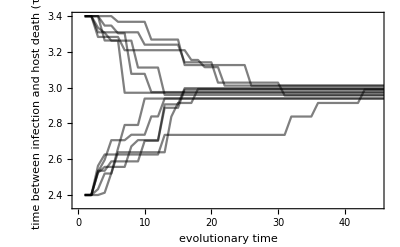

```mathematica
ListLinePlot[{τr1,τr2,τr3,τr4,τr5,τr6,τr7,τr8,τr9,τr10,τr11,τr12},Frame->True,FrameLabel->{{Style["time between infection\n and host death (τ)",16,FontFamily->"Helvetica"],None},{Style["evolutionary time",16,FontFamily->"Helvetica"],Style["parasites drive quasiperiodic dynamics",16,FontFamily->"Helvetica"]}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0,45},All},FrameStyle->14]
```

```mathematica
τrx=Join[{τr1},{τr2},{τr3},{τr4},{τr5},{τr6}];
τry=Join[{τr7},{τr8},{τr9},{τr10},{τr11},{τr12}];
list1=Table[{x=Length@Select[list, # >= 2.9 &];
y=51-x},{list,τrx}]
list2=Table[{x=Length@Select[list, # <= 3 &];
y=51-x},{list,τry}]
```

{{14},{15},{9},{12},{12},{35}}

{{10},{6},{51},{12},{51},{30}}

```mathematica
list1x=Flatten@list1;
list2x=Flatten@list2;
N@Mean@Join[list1x,list2x]
```

21.4167

it takes 21.4 mutants on average to get within 0.05 of τ^* = 2.95

in the simulation that will run from the code below, the emerging host cohort is constant each season and thus the dynamics will not cycle

```mathematica
ClearAll["Global`*"]
(*τ=2.4;*) τ=3.4; v10=1;  b=200; a=3.5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001;
j1[t_,tl_]:=If[0<t<tl,1/tl,0];
sol := NDSolve[{
D[s1[t], t]==10^8 j1[t,tl]-d s1[t]-a *s1[t]*v1[t],
D[v2[t], t]== a b Exp[-d τ]*s1[t-τ]*v1[t-τ]-δ v2[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,v1[t/;t≤0]==v10,v2[t/;t≤0]==0}, 
{s1,v1,v2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
 v2total = {v10}; 
For[y=0, y<100,y++,
sol1=sol;
v10 = v2[T]/.sol1[[1,3]];
v2total=Append[v2total, v10];
v20eq=Last[v2total];
];
(*dynamics do not as τ increases parasite density because the host population is constant*)
ListPlot[{v2total},Frame->True,FrameLabel->{{"parasite density",None},{"season","T=4, t_l=1"}}];
```

```mathematica
(*set up vars and differential equations, for n strains*)
 Subscript[v10,1]=v20eq;
vars:=Table[{Subscript[v2,j],Subscript[v1,j],s1},{j,n}];
eqns:={s1'[t]==10^8 j1[t,tl]-d s1[t]-a *s1[t] (Sum[Subscript[v1,k][t] ,{k,n}]),Table[{Subscript[v2,j]'[t]==a b Exp[-d Subscript[τ,j]]*s1[t-Subscript[τ,j]]*Subscript[v1,j][t-Subscript[τ,j]]-δ Subscript[v2,j][t],
Subscript[v1,j]'[t]==-δ Subscript[v1,j][t]},{j,n}]};
(*initial ICs*)
ics={Subscript[v1,1][t/;t≤0]==Subscript[v10,1],Subscript[v2,1][t/;t≤0]==0,s1[t/;t≤0]==0};
τr={τ};τm={};

(*main loop*)
Monitor[Do[(*Subscript[τ,1]=2.4;*) Subscript[τ,1]=3.4; v10m=1; s0=10^8;  b=200; a=3.5*10^-7;  δ=2; d=0.25;  tl=1;T=4; σ=500; α=0.0001; nx=RandomInteger[{1000,1100}];
j1[t_,tl_]:=If[0<t<tl,1/tl,0];Do[(*follows dynamics of n strains for nx seasons*)
sol=NDSolve[{Flatten[eqns],Flatten[Join[{s1[t/;t≤0]==0},Flatten[Table[{Subscript[v1,j][t/;t≤0]==Subscript[v10,j],Subscript[v2,j][t/;t≤0]==0},{j,n}]]]]},Flatten[vars],{t,0,T}][[1]];
Table[If[Evaluate[Subscript[v2,j][T]/.sol]<1,Subscript[v10,j] =0,Subscript[v10,j] =Evaluate[Subscript[v2,j][T]/.sol]],{j,n}];
s0 = Evaluate[σ s1[T]/(1+ α s1[T])/.sol];
If[Subscript[v10,n]<1,Break[]];,nx];
(*set τ for n=n+1 strains (mutates strain with highest density)*)
list=Table[Subscript[v10,j],{j,n}];
Subscript[τ,n+1]=Subscript[τ,First@Flatten[Position[list,Max[list]]]]+RandomVariate[NormalDistribution[0,0.1]];
τr=Append[τr,Subscript[τ,First@Flatten[Position[list,Max[list]]]]];
τm=Append[τm,Subscript[τ,n+1]];
(*set ic for n=n+1 strain*)
Subscript[v10,n+1]=1
,{n,45}],{n,τr,τm}]
```

simulations 1-6 started with τ_1 = 2.4, simulations 7-12 started with τ_1 = 3.4

```mathematica
τr
```

{3.4,3.4,3.19031,3.0817,3.02743,3.02743,3.02743,3.02743,3.02743,3.02743,3.02743,3.02743,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016,3.0016}

```mathematica
τr1=τr;
τm1=τm;
Export["trsimsnc1.mx",τr1]
Export["tmsimsnc1.mx",τm1]
```

trsimsnc1.mx

tmsimsnc1.mx

```mathematica
τr2=τr;
τm2=τm;
Export["trsimsnc2.mx",τr2]
Export["tmsimsnc2.mx",τm2]
```

trsimsnc2.mx

tmsimsnc2.mx

```mathematica
τr3=τr;
τm3=τm;
Export["trsimsnc3.mx",τr3]
Export["tmsimsnc3.mx",τm3]
```

trsimsnc3.mx

tmsimsnc3.mx

```mathematica
τr4=τr;
τm4=τm;
Export["trsimsnc4.mx",τr4]
Export["tmsimsnc4.mx",τm4]
```

trsimsnc4.mx

tmsimsnc4.mx

```mathematica
τr5=τr;
τm5=τm;
Export["trsimsnc5.mx",τr5]
Export["tmsimsnc5.mx",τm5]
```

trsimsnc5.mx

tmsimsnc5.mx

```mathematica
τr6=τr;
τm6=τm;
Export["trsimsnc6.mx",τr6]
Export["tmsimsnc6.mx",τm6]
```

trsimsnc6.mx

tmsimsnc6.mx

```mathematica
τr7=τr;
τm7=τm;
Export["trsimsnc7.mx",τr7]
Export["tmsimsnc7.mx",τm7]
```

trsimsnc7.mx

tmsimsnc7.mx

```mathematica
τr8=τr;
τm8=τm;
Export["trsimsnc8.mx",τr8]
Export["tmsimsnc8.mx",τm8]
```

trsimsnc8.mx

tmsimsnc8.mx

```mathematica
τr9=τr;
τm9=τm;
Export["trsimsnc9.mx",τr9]
Export["tmsimsnc9.mx",τm9]
```

trsimsnc9.mx

tmsimsnc9.mx

```mathematica
τr10=τr;
τm10=τm;
Export["trsimsnc10.mx",τr10]
Export["tmsimsnc10.mx",τm10]
```

trsimsnc10.mx

tmsimsnc10.mx

```mathematica
τr11=τr;
τm11=τm;
Export["trsimsnc11.mx",τr11]
Export["tmsimsnc11.mx",τm11]
```

trsimsnc11.mx

tmsimsnc11.mx

```mathematica
τr12=τr;
τm12=τm;
Export["trsimsnc12.mx",τr12]
Export["tmsimsnc12.mx",τm12]
```

trsimsnc12.mx

tmsimsnc12.mx

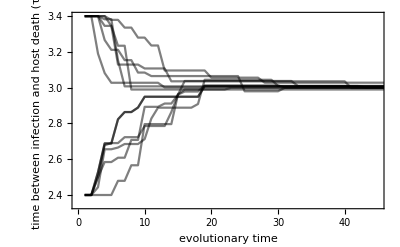

```mathematica
ListLinePlot[{τr1,τr2,τr3,τr4,τr5,τr6,τr7,τr8,τr9,τr10,τr11,τr12},Frame->True,FrameLabel->{{Style["time between infection\n and host death (τ)",16,FontFamily->"Helvetica"],None},{Style["evolutionary time",16,FontFamily->"Helvetica"],Style["dynamics remain stable",16,FontFamily->"Helvetica"]}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0,45},All},FrameStyle->14]
```

```mathematica
τrx=Join[{τr1},{τr2},{τr3},{τr4},{τr5},{τr6}];
τry=Join[{τr7},{τr8},{τr9},{τr10},{τr11},{τr12}];
list1=Table[{x=Length@Select[list, # >= 2.95 &];
y=46-x},{list,τrx}]
list2=Table[{x=Length@Select[list, # <= 3.05 &];
y=46-x},{list,τry}]
```

{{18},{13},{14},{18},{14},{14}}

{{6},{24},{27},{13},{7},{4}}

```mathematica
list1x=Flatten@list1;
list2x=Flatten@list2;
N@Mean@Join[list1x,list2x]
```

14.3333

it takes 14.3 mutants on average to get within 0.05 of τ^* = 3